## Averaged Circuit Eigenvalue Sampling

## Simulations of ACES with 1D circuits

### Function definitions

These are the primitive Clifford gates (excluding measurement) for which we’ll model the noise. The GateNames variable is a list of names of the gates. The XC gate is the CX gate with the control and target reversed. The single-qubit gates are labeled by the permutation that they induce on XYZ, ignoring signs. So, for example, the fourth gate is the Hadamard gate (H) and the fifth is the phase gate (S). All of these gates ignore the overall phase of the Pauli basis since this can always be corrected afterwards. For example, the inverse of S is itself up to a Pauli gate (S^2==Z). So for mirror circuits (where we never need to track the ± signs) we can just keep track of the matrix action below. These gates act on the binary vector with the basis order {x_1,z_1,x_2,z_2}.

```mathematica
GateNames={"CX","XC","XYZ","ZYX","YXZ","XZY","ZXY","YZX","Measure"};
Gates={({{1, 0, 0, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}}),({{1, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 1}}),({{1, 0}, {0, 1}}),({{0, 1}, {1, 0}}),({{1, 0}, {1, 1}}),({{1, 1}, {0, 1}}),({{0, 1}, {1, 1}}),({{1, 1}, {1, 0}})};
InverseGates=Inverse[#,Modulus->2]&/@Gates;
AllOneQubitGates=Flatten[Position[Length/@Gates,_?(#==2&)]];
AllTwoQubitGates=Flatten[Position[Length/@Gates,_?(#==4&)]];
NumberOfOneQubitGates=Length[AllOneQubitGates];
NumberOfTwoQubitGates=Length[AllTwoQubitGates];
GateInversion[k_]:=GateInversion[k]=PermutationReplace[k,FindPermutation[Gates,InverseGates]];
Do[GateInversion[k],{k,0,NumberOfOneQubitGates+NumberOfTwoQubitGates+1}];
G[0]=Nothing;
Do[G[k]=Gates⟦k⟧;,{k,Length[Gates]}];
```

Our circuits are 1D circuits that have randomly alternating layers of 1-qubit gates and 2-qubit gates. The 2-qubit gate layers tile the 1D chain and alternate between starting on the first or second qubit. Extra space on the boundary is labeled with random one-qubit gates. Note that our circuits are not ragged arrays: we pad by 0 when there is a two-qubit gate. We wouldn’t save much space by using ragged arrays since the circuits are dense, and it would complicate the code later on to deal with ragged arrays. The last function inserts a layer that tiles the chain with the exact same gate (possibly with an offset).

```mathematica
RandomOneQubitLayer[n_Integer]:=RandomChoice[AllOneQubitGates,n];

RandomTwoQubitLayer[n_Integer,offset_Integer]:=Module[{t,o=Mod[offset,2]},
t=RandomChoice[AllTwoQubitGates,Floor[(n+o)/2]-o];
t=Riffle[t,0,{2,-1,2}];
If[OddQ[n+o],AppendTo[t,RandomChoice[AllOneQubitGates]];];
If[o==1,PrependTo[t,RandomChoice[AllOneQubitGates]];];
Return[t];
];
```

This function forms a sparse direct sum of the matrices in the list c. This effectively compiles each circuit layer into a specific matrix.

```mathematica
DirectSum[c_List]:=SparseArray[Band[{1,1}]->{##}]&@@(G/@c);
```

We can create a random circuit on n qubits having depth d as a matrix whose rows are alternating circuit layers. We can introduce more randomness by choosing each layer at random (RandomCircuit2). Finally, we can run a circuit where a specific gate layer is interleaved into the circuit.

```mathematica
RandomCircuit[n_Integer,d_Integer]:=Table[If[OddQ[k],RandomOneQubitLayer[n],RandomTwoQubitLayer[n,Mod[k/2-1,2]]],{k,d}];

RandomCircuit2[n_Integer,d_Integer]:=Table[If[OddQ[RandomInteger[]],RandomOneQubitLayer[n],RandomTwoQubitLayer[n,RandomInteger[]]],{d}];
```

The next function takes a circuit and computes its “mirror”, i.e., the time reverse of the original circuit, with total depth d. If d is odd it adds an extra layer of random one-qubit gates.

```mathematica
InverseCircuit[c_?MatrixQ]:=Map[GateInversion,Reverse[c],{2}];

RandomMirrorCircuit[n_Integer,d_Integer]:=Module[{t},
t=RandomCircuit[n,Floor[d/2]];
t=Join[t,InverseCircuit[t]];
If[EvenQ[d],
Return[t];,
Return[Join[t,{RandomOneQubitLayer[n]}]];
];
];

RandomMirrorCircuit2[n_Integer,d_Integer]:=Module[{t},
t=RandomCircuit2[n,Floor[d/2]];
t=Join[t,InverseCircuit[t]];
If[EvenQ[d],
Return[t];,
Return[Join[t,{RandomOneQubitLayer[n]}]];
];
];
```

CircuitHistory writes the net action of the circuit for each time step. PauliHistory finds the entire history of the circuit action acting on the standard Pauli basis. So, of p=PauliHistory[c], then p⟦1⟧ is the action on x_1, etc.  The Pauli history is labeled as p⟦Pauli, Time, Space⟧, in other words.

```mathematica
CircuitHistory[c_?MatrixQ]:=Module[{cc},
cc=DirectSum/@c;
Return[FoldList[Mod[Dot[#2,#1],2]&,cc]];
];

PauliHistory[c_?MatrixQ]:=Transpose[Join[{IdentityMatrix[2n,SparseArray]},CircuitHistory[c]],{2,3,1}];
```

This function chooses at random a set of n single-qubit Pauli matrices that defines a local basis. These will be the probe states for the ACES experiments. We can also get a list of all the 3n single-qubit Paulis that we might use as probes, and a list of all Paulis of weight at most two.

```mathematica
KNNPaulis[n_Integer,k_Integer]:=SparseArray[DeleteDuplicates[Flatten[Table[RotateRight[PadRight[IntegerDigits[m,2,2k],2n],2j],{j,0,n-k},{m,4^k-1}],1]]];
```

Given a Clifford circuit, the next function tracks the Pauli frame through the circuit layer by layer beginning with the input Pauli P. The vector P is a binary array in the basis {x_1,z_1,x_2,z_2,...,x_n,z_n}. We ignore the overall ±1 signs since we can always correct for this in postprocessing.

This function defines an array of variables labeled x[G, q,2 x_q+z_q] for single-qubit gates and similarly for two-qubit gates x[G, q1,FromDigits[{x_q1,z_q1,x_q2,z_q2},2]]. The first label is the gate, the second label is the first qubit that the gate acts on, and the third label is the integer formed from the 2n-bit string labeling the Pauli eigenvalue. This is hard coded for 2 two-qubit gates, 6 one-qubit gates and a measurement gate.

Given a Pauli or a list of Paulis P, compute the symbolic circuit log-eigenvalue as a function of the log-eigenvalues of the noisy circuit elements. The variable x is used to label the circuit log-eigenvalues and c is the circuit. The first function is a helper function that splits each Pauli in the Pauli history into Paulis that are “commensurate” with the gates they encounter at this time step. So, if a Pauli will encounter a two-qubit gate or a one-qubit gate, it will group the Pauli history accordingly and return a Pauli from one of 16 or 4 choices, respectively.

This function returns a list that describes each circuit layer as single-qubit (1), two-qubit with no offset (2), or two-qubit with an offset (3).

```mathematica
CircuitLayerType[c_?MatrixQ]:=Table[Which[c⟦k,1⟧≤NumberOfTwoQubitGates,2,c⟦k,2⟧≤NumberOfTwoQubitGates,3,True,1],{k,Length[c]}];

CircuitPauliPartition[c_?MatrixQ,p_?ArrayQ,n_Integer]:=Module[{t,tL,tt={0,0,0},pp,j},
t=Flatten[Position[CircuitLayerType[c],#]]&/@{1,2,3};
tL=Length/@t;
tt⟦1⟧=SparseArray[Band[{1,1}]->{##}]&@@(ConstantArray[{{2},{1}},{n}]);

If[OddQ[n],
tt⟦2⟧=SparseArray[Band[{1,1}]->{##}]&@@(Join[ConstantArray[{{8,0},{4,0},{2,0},{1,0}},{Floor[n/2]}],{{{2},{1}}}]);
tt⟦3⟧=SparseArray[Band[{1,1}]->{##}]&@@(Join[{{{2},{1}}},ConstantArray[{{8,0},{4,0},{2,0},{1,0}},{Floor[n/2]}]]);,
tt⟦2⟧=SparseArray[Band[{1,1}]->{##}]&@@(ConstantArray[{{8,0},{4,0},{2,0},{1,0}},{n/2}]);
tt⟦3⟧=SparseArray[Band[{1,1}]->{##}]&@@(Join[{{{2},{1}}},ConstantArray[{{8,0},{4,0},{2,0},{1,0}},{n/2-1}],{{{2},{1}}}]);
];

pp=SparseArray[{2n,Length[c],n}->0];

For[j=1,j≤3,j++,
If[tL⟦j⟧>0,
pp⟦All,t⟦j⟧⟧=p⟦All,t⟦j⟧,All⟧.tt⟦j⟧;
];
];
Return[pp];
];

Arow[c_?MatrixQ,cpp_?ArrayQ,ip_?VectorQ,x_Symbol]:=Module[{cases,keys,values},
cases=ArrayRules[SparseArray[Tr[cpp⟦ip⟧,BitXor,1]]];
keys=Most[Keys[cases]];
values=Most[Values[cases]];
Return[Total[x@@#&/@({Extract[c,#]&/@keys,keys⟦All,2⟧,values}ᵀ)]];
];

Amat[c_?MatrixQ,cpp_?ArrayQ,ip_?MatrixQ]:=With[{n=Dimensions[c]⟦2⟧,P=Flatten[Keys[Most[ArrayRules[#]]]]&/@ip},
Return[CoefficientArrays[Table[Arow[c,cpp,P⟦k⟧,x],{k,Length[ip]}],GateVariables[n,x]]⟦2⟧];
];
```

If we want the model to be a little coarser than allowing arbitrary errors on each gate, we can reduce some of the model parameters. 

Here is a new function that tries to give the model as a parameter. It is a string that says which error parameters are allowed as we vary the gate “G”, the qubit that it acts on “Q”, and the Pauli eigenvalue “P”. The full model is given by the string “GQP” and is the default. The minimal model given by the empty string “”, has only three parameters and varies only with single-qubit gate, two-qubit gate, and measurement. 

In this notebook, we consider the “maximal” model of noise which is time-stationary, uncorrelated, and with zero leakage. By this we mean that the noise does not depend on the time step (time-stationary) or on the other adjacent gates (uncorrelated), and the Pauli eigenvalue associated to the identity is 1 for every noise channel. Obviously, larger models that take these time- and space-like correlations as well as leakage into account could be formulated in this same framework, but we do not consider that here. Instead, we also consider more parsimonious models that reduce the number of parameters from the maximal model. 

In the maximal model, each noise parameter is specified by a gate “G”, the qubit(s) “Q” upon which the gate acts, and the specific Pauli eigenvalue “P” in the corresponding noise channel. To specify a reduced model, we input a string that tells us which of these dependencies to marginalize over. To keep things as simple as possible, this code can only marginalize over the entirety of one or more of these dependencies. So for example, we cannot at this time marginalize separately on specific gate or qubit dependencies, or over (say) X and Y errors separate from Z errors, even though these are reasonable models to consider. It would be straightforward to add this functionality, but we leave this to future work. 

The variable model is a string that is a subset of “GQP” in any order. WHen the model is maximal, nothing is marginalized over: model = "". If “G” is present, then the type of gate is marginalized except for whether the gate is a 1-qubit, 2-qubit, or measurement gate. If “Q” is present, then the qubit that the gate acts on is marginalized. If “P” is present, then the type of Pauli eigenvalue is marginalized (that is, we effectively assume local depolarizing noise on each gate). If no model is specified, we default to the maximal model. 

We also allow specifying to marginalize just over the Pauli degree of freedom on the measurements only, “M”. This is useful if the measurement error doesn’t depend on the basis in which the measurement takes place.

```mathematica
GateVariables[n_Integer]:=GateVariables[n,""];

GateVariables[n_Integer,model_String]:=Module[{m=StringPartition[model,1],a={{1},{1},{1}},b={{NumberofTwoQubitGates+1},{1},{1}},c={{NumberOfOneQubitGates+NumberOfTwoQubitGates+1},{1},{1}}},
If[Not[SubsetQ[m,{"G"}]],a⟦1⟧=AllTwoQubitGates; b⟦1⟧=AllOneQubitGates;];If[Not[SubsetQ[m,{"Q"}]],a⟦2⟧=Range[n-1]; b⟦2⟧=Range[n]; c⟦2⟧=Range[n];];
If[Not[SubsetQ[m,{"P"}]],a⟦3⟧=Range[4^2-1]; b⟦3⟧=Range[4^1-1];];
If[Not[SubsetQ[m,{"M"}]],c⟦3⟧=Range[4^1-1];];
Return[Join[Tuples[a],Tuples[b],Tuples[c]]];
];

GateVariables[n_Integer,x_Symbol]:=GateVariables[n,x,""];

GateVariables[n_Integer,x_Symbol,model_String]:=Apply[x,GateVariables[n,model],1];
```

This takes the full matrix A and marginalizes it to one of the smaller models.

```mathematica
Pmarg[{i_Integer,j_Integer,k_Integer}]:={i,j,1};
Qmarg[{i_Integer,j_Integer,k_Integer}]:={i,1,k};
Mmarg[{i_Integer,j_Integer,k_Integer}]:={i,j,If[i>NumberOfOneQubitGates+NumberOfTwoQubitGates,1,k]};
Gmarg[{i_Integer,j_Integer,k_Integer}]:={Which[i≤NumberOfTwoQubitGates,1,i≤NumberOfOneQubitGates+NumberOfTwoQubitGates,2,True,3],j,k};

MarginalizeA[A_?MatrixQ,n_Integer,""]:=A;

MarginalizeA[A_?MatrixQ,n_Integer,model_String]:=Module[{row,col,m=StringPartition[model,1],pos},
col=GateVariables[n];
If[SubsetQ[m,{"Q"}],col=Qmarg/@col;];
If[SubsetQ[m,{"P"}],col=Pmarg/@col;];
If[SubsetQ[m,{"M"}],col=Mmarg/@col;];
If[SubsetQ[m,{"G"}],col=Gmarg/@col;];
row=Values[PositionIndex[col]];
col={Range[Length[row]]}ᵀ;
pos=Flatten[Table[Tuples[{row⟦k⟧,col⟦k⟧}],{k,Length[row]}],1];
Return[A.SparseArray[Thread[pos->1]]];
];
```

### Generating random circuits

In the gate set that we are considering, there are 51n-30 different variables in the model. We need to pick enough Paulis to send through enough circuits so that we have at least this many equations. Note that we want to preferentially look at low-weight Paulis since these typically require fewer samples to resolve. To keep things as simple as possible, we will only look at k nearest neighbors at the input, and we use k=1 or 2. Instead of using exact mirror circuits, we add a small random layer of depth r to a perfect mirror circuit, and we use r≤5. This means that each Pauli channel eigenvalue that we estimate will have weight at most k+r+1. 

Here is the procedure we used to generate some random circuits. 

With the constraints on k and r above, we sample random circuits of varying depths until the design matrix A is full rank. Since each random circuit adds O(n) rows to A and A has only O(n) columns, we expect that we only need O(1) random circuits before the rank saturates. We pick a series of depths by hand, starting with a few very low-depth circuits, and then adding depth according to the Fibonacci series. We try to keep the maximum depth not much larger than n. After trying 100 times, we change the parameters a little and try again. The circuits are stacked into a matrix M that has measurement layers built into it. Together with the list of which circuits have which Pauli locality (k=1 or k=2 for each circuit, stored in the variable kk), this is enough to reproduce the calculation. We store A and n too for ease of use. The example below is for n=10.

This is all done by hand, so obviously there is room for improvement!

```mathematica
n=10;r=4;j=0;m=Length[GateVariables[n]];rank=0;jmax=100;
While[rank≠m∧j<jmax,
j++;A={};M={};
dd={2,2,2,2,2,3,5,8,13,21};
kk=ConstantArray[1,Length[dd]]; 
kk⟦{1,2,3,4}⟧=2;
For[d=1,d≤Length[dd],d++,
c=RandomMirrorCircuit[n,dd⟦d⟧];
c2=RandomCircuit2[n,r];
c=Join[c,c2];
p=PauliHistory[c];
cm=Join[c,{ConstantArray[NumberOfOneQubitGates+NumberOfTwoQubitGates+1,n]}];
cpp=CircuitPauliPartition[cm,p,n];
P=KNNPaulis[n,kk⟦d⟧];
AA=Amat[cm,cpp,P];
A=Join[A,AA];
M=Join[M,cm];
];
rank=MatrixRank[N[A]];
Print["On try j = ",j,", the rank ratio is = ",rank,"/",m,"."];
];
If[rank==m,
Print["\n----------------\n  🐺 Success! 🐺\n----------------"];
Print["For n = ",n,", the depths and input Pauli weights are:\n",TableForm[{kk,dd},TableHeadings->{{"k","d"}, None}]];
Print["Total number of circuits = ",Length[dd],"\nAdd random layer of depth r = ",r,"\nTotal circuit length = ",Total[dd+r]];
Print["Total number of estimated fidelities = ",Dimensions[A]⟦1⟧];,
Print["\n----------------\n  ☹ Failure. ☹\n----------------\nTry again with different parameters."]
];
```

On try j = 1, the rank ratio is = 472/480.

On try j = 2, the rank ratio is = 477/480.

On try j = 3, the rank ratio is = 460/480.

On try j = 4, the rank ratio is = 475/480.

On try j = 5, the rank ratio is = 430/480.

On try j = 6, the rank ratio is = 420/480.

On try j = 7, the rank ratio is = 480/480.

----------------
  🐺 Success! 🐺
----------------

For n = 10, the depths and input Pauli weights are:
k | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
d | 2 | 2 | 2 | 2 | 2 | 3 | 5 | 8 | 13 | 21

Total number of circuits = 10
Add random layer of depth r = 4
Total circuit length = 100

Total number of estimated fidelities = 624

Now we can save the data from this calculation. All we need to do the simulations is A, but storing the circuits M and kk will make the calculation reproducible.

```mathematica
SetDirectory[NotebookDirectory[]<>"/data/"];
Save["n="<>ToString[n]<>",kk,dd,M,A.txt",{n,kk,dd,M,A}]
```

### Visualizing a Pauli going through a circuit

This function takes a circuit c (without a final measurement round) and produces a plot of the Pauli propagation through the circuit. The second argument is a binary vector P, and it returns the history of that Pauli with time going down.

```mathematica
HistoryPlot[c_List,P_?VectorQ]:=Module[{colors,p,h,hp},
colors=RGBColor/@{"#CD6355","#22B6DB","#ECCD3E"};
p=PauliHistory[c];
h=Partition[#,2]&/@Mod[P.p,2];
hp=Map[FromDigits[#,2]&,h,{2}];
Return[ArrayPlot[hp,ColorRules->{0->None,1->colors⟦1⟧,2->colors⟦2⟧,3->colors⟦3⟧}]];
];
```

Here is an example. This code produces a circuit c. The c below is used in the figure in the paper.

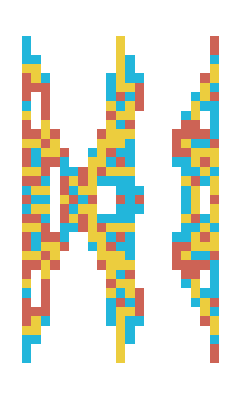

```mathematica
k=8;
n=Fibonacci[k];
d=Fibonacci[k+1];
c=RandomMirrorCircuit[n,d];
P=ConstantArray[0,{2n}];
P⟦{1,n,n+1,2n}⟧=1;
HistoryPlot[c,P]
```

```mathematica
c={{5,4,4,7,8,4,3,4,5,4,5,8,6,5,5,8,7,8,5,7,8},{2,0,1,0,1,0,1,0,2,0,1,0,1,0,2,0,2,0,1,0,7},{8,3,7,4,5,8,5,3,4,6,5,6,8,7,6,6,5,5,8,6,4},{7,2,0,1,0,2,0,1,0,1,0,2,0,1,0,2,0,2,0,2,0},{6,8,8,3,5,4,4,7,7,7,3,4,3,8,8,8,7,6,7,5,8},{1,0,1,0,1,0,1,0,2,0,2,0,1,0,2,0,1,0,2,0,6},{3,4,4,3,3,4,8,3,6,5,6,4,8,3,5,3,3,3,8,7,8},{5,1,0,2,0,2,0,2,0,1,0,2,0,2,0,1,0,2,0,2,0},{6,3,7,6,8,3,5,8,7,7,5,4,4,3,7,4,3,8,4,5,5},{1,0,2,0,2,0,1,0,2,0,1,0,1,0,1,0,1,0,1,0,4},{6,7,6,7,4,7,4,6,3,3,4,4,3,3,5,4,8,3,4,3,4},{7,2,0,2,0,1,0,1,0,2,0,2,0,2,0,1,0,2,0,1,0},{5,5,4,7,6,4,8,4,8,8,8,7,5,8,8,3,5,8,8,5,7},{2,0,2,0,2,0,2,0,2,0,2,0,1,0,2,0,1,0,2,0,4},{3,7,3,4,5,8,8,7,3,3,8,8,6,3,4,4,3,4,6,7,5},{4,2,0,1,0,2,0,2,0,2,0,1,0,2,0,1,0,1,0,1,0},{8,4,6,5,8,6,4,3,5,5,4,3,6,6,6,3,3,7,3,3,5},{7,4,6,5,7,6,4,3,5,5,4,3,6,6,6,3,3,8,3,3,5},{4,2,0,1,0,2,0,2,0,2,0,1,0,2,0,1,0,1,0,1,0},{3,8,3,4,5,7,7,8,3,3,7,7,6,3,4,4,3,4,6,8,5},{2,0,2,0,2,0,2,0,2,0,2,0,1,0,2,0,1,0,2,0,4},{5,5,4,8,6,4,7,4,7,7,7,8,5,7,7,3,5,7,7,5,8},{8,2,0,2,0,1,0,1,0,2,0,2,0,2,0,1,0,2,0,1,0},{6,8,6,8,4,8,4,6,3,3,4,4,3,3,5,4,7,3,4,3,4},{1,0,2,0,2,0,1,0,2,0,1,0,1,0,1,0,1,0,1,0,4},{6,3,8,6,7,3,5,7,8,8,5,4,4,3,8,4,3,7,4,5,5},{5,1,0,2,0,2,0,2,0,1,0,2,0,2,0,1,0,2,0,2,0},{3,4,4,3,3,4,7,3,6,5,6,4,7,3,5,3,3,3,7,8,7},{1,0,1,0,1,0,1,0,2,0,2,0,1,0,2,0,1,0,2,0,6},{6,7,7,3,5,4,4,8,8,8,3,4,3,7,7,7,8,6,8,5,7},{8,2,0,1,0,2,0,1,0,1,0,2,0,1,0,2,0,2,0,2,0},{7,3,8,4,5,7,5,3,4,6,5,6,7,8,6,6,5,5,7,6,4},{2,0,1,0,1,0,1,0,2,0,1,0,1,0,2,0,2,0,1,0,8},{5,4,4,8,7,4,3,4,5,4,5,7,6,5,5,7,8,7,5,8,7}};
```

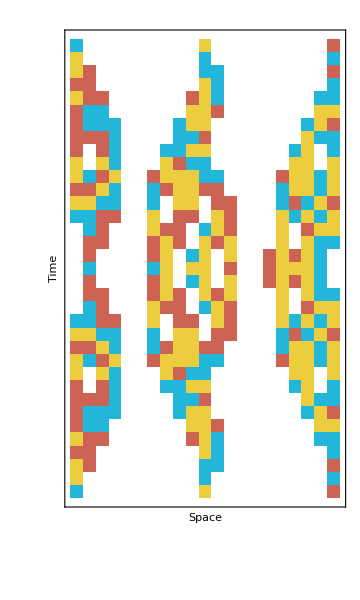

```mathematica
hp=HistoryPlot[c,P];
Show[hp,Background->None,ImageSize->Medium,Frame->True,FrameStyle->{{Directive[Opacity[1],FontOpacity->1],Directive[Opacity[0],FontOpacity->1]},{Directive[Opacity[1],FontOpacity->1],Directive[Opacity[0],FontOpacity->1]}},FrameLabel->{"Space","Time","X                                    Y                                    Z",None},FrameTicks->None,LabelStyle->{FontFamily->"Lato",14,GrayLevel[0]}]
```

## Numerical reconstruction

### More function definitions

Generates a uniform sample from the d dimensional simplex.

```mathematica
RandomSimplex[d_Integer]:=Differences[Join[{0},Sort[Table[RandomReal[],{d-1}]],{1}]];
```

Projects a vector p onto the closest point (in l_2 distance) to the n-dimensional simplex in O(n Log[n]) time. The second version mixes this point with a uniform distribution of total mass ϵ.

```mathematica
ProjectSimplex[p_?VectorQ]:=Module[{n=Length[p],m=Sort[p,Greater],r,t},
r=Max[Range[n] Boole[Thread[m-(Accumulate[m]-1)/Range[n]>0]]];
t=(Total[m⟦1;;r⟧]-1)/r;
Return[Max[#,0]&/@(p-t)];
];

ProjectSimplex[p_?VectorQ,ϵ_?NumberQ]:=
With[{n=Length[p]},(1-ϵ) ProjectSimplex[p]+ConstantArray[ϵ/n,n]];
```

The Walsh-Hadamard Transform. It transforms from a Pauli probability distribution to the corresponding Pauli channel eigenvalues. The inverse transformation is the same, except you divide the result by Length[x].

```mathematica
W[x_?VectorQ]:=√Length[x] DiscreteHadamardTransform[x,Method->"BitComplement"];
```

#### Building a gate error model

For a numerical simulation, we have to assign noise to each of these 51n-30 gates. We use the following parameters roughly estimated from the Arute et al. (2019) experiment. Single-qubit gates have a characteristic error rate of 0.15%, two-qubit gates have an error rate of 0.36%, and (uncorrelated) measurement errors occur with error rate 3.1%. We assign fluctuations to these numbers by sampling uniformly in the interval between ×2  and ×1/2 of these values.

Here are the total error rates.

```mathematica
err={0.0015,0.0036, 0.031};
ϵ={RandomReal[{.5,2} err⟦2⟧,2n-2],RandomReal[{.5,2} err⟦1⟧,6n],RandomReal[{.5,2} err⟦3⟧,n]};
```

To get the “true” error rates, we sample randomly from the simplex of size 3 (for one-qubit gates or measurements) and size 15 (for two-qubit gates).

```mathematica
p2q=Join[{1-ϵ⟦1⟧},(ϵ⟦1⟧*Table[RandomSimplex[4^2-1],2n-2])ᵀ]ᵀ;
p1q=Join[{1-ϵ⟦2⟧},(ϵ⟦2⟧*Table[RandomSimplex[4^1-1],6n])ᵀ]ᵀ;
pm=Join[{1-ϵ⟦3⟧},(ϵ⟦3⟧*Table[RandomSimplex[4^1-1],n])ᵀ]ᵀ;
ptrue={p2q,p1q,pm};
```

The individual gate Pauli channel eigenvalues are given by the Hadamard transform of these true probabilities.

```mathematica
{λ2q,λ1q,λm}=Map[W,ptrue,{2}];
λtrue={λ2q,λ1q,λm};
```

The true values for X are given by dropping the first eigenvalue (corresponding to the identity Pauli) and taking -Log, and the true values for the circuit Pauli channel eigenvalues (btrue) are solvable from this since we know the design matrix A.

```mathematica
Xtrue=Flatten[Map[-Log[Rest[#]]&,λtrue,{2}]];
btrue=A.Xtrue;
```

Now that we know the parameters of the true model, we can estimate the precision of an estimator given some number of samples. Let S be the number of samples in one circuit with one Pauli basis. Then the total number of samples taken is S×Length[A]/n, since we get n eigenvalues per experiment.

```mathematica
S=20000;
```

We sample the each Pauli S times to get a binomial random variable Binom[S,p], where p=(1+Exp[-btrue])/2. Therefore we use the sample mean μ of this and look at -Log[2μ-1] as our estimator for b. Note that this is justified even if we sample the ± eigenstates and then difference the counts. This is because if X~Binom[S/2,p] and Y~Binom[S/2,1-p], then S/2+X-Y~Binom[S,p].

```mathematica
best=(-Log[2.0/S RandomVariate[BinomialDistribution[S,#]]-1]&/@((1+Exp[-btrue])/2));
```

All of this gets encapsulated in the following functions:

```mathematica
CreateModel[n_Integer,err_?VectorQ]:=Module[{ϵ,p2q,p1q,pm,ptrue,λtrue,Xtrue,btrue,best},
ϵ={RandomReal[{.5,2} err⟦2⟧,2n-2],RandomReal[{.5,2} err⟦1⟧,6n],RandomReal[{.5,2} err⟦3⟧,n]};p2q=Join[{1-ϵ⟦1⟧},(ϵ⟦1⟧*Table[RandomSimplex[4^2-1],2n-2])ᵀ]ᵀ;
p1q=Join[{1-ϵ⟦2⟧},(ϵ⟦2⟧*Table[RandomSimplex[4^1-1],6n])ᵀ]ᵀ;
pm=Join[{1-ϵ⟦3⟧},(ϵ⟦3⟧*Table[RandomSimplex[4^1-1],n])ᵀ]ᵀ;
ptrue={p2q,p1q,pm};
λtrue=Map[W,ptrue,{2}];Xtrue=Flatten[Map[-Log[Rest[#]]&,λtrue,{2}]];
Return[{Flatten[ptrue,1],Xtrue}];
];

SampleModel[A_?MatrixQ,Xtrue_?VectorQ,S_Integer]:=With[{btrue=A.Xtrue},Return[-Log[2.0/S RandomVariate[BinomialDistribution[S,#]]-1]&/@((1+Exp[-btrue])/2)];
];
```

This function converts an estimate Xest of X into an estimate of the error probabilities.

```mathematica
ProbEst[Xest_?VectorQ,n_Integer,δ_:0]:=Module[{Λest,λ1,λ2},
Λest=Exp[-Xest];
λ2=Join[{1},#]&/@Partition[Λest⟦1;;(4^2-1) (2n-2)⟧,4^2-1];
λ1=Join[{1},#]&/@Partition[Λest⟦(4^2-1) (2n-2)+1;;⟧,4^1-1];
Return[ProjectSimplex[#,δ]&/@(W/@Join[λ2/16,λ1/4])];
];
```

### Performance

If we quit, we can load A back from the file. Since we are working with the no-leakage model, we can just solve for A by looking at the number of variables.

```mathematica
n=100;
SetDirectory[NotebookDirectory[]<>"/data/"];
Get["n="<>ToString[n]<>",kk,dd,M,A.txt"];
Print["Loading data for circuit list M with\nn = ",n,",\nkk = ",kk,",\ndd = ",dd,",\nA = ",A,"."];
```

Loading data for circuit list M with
n = 100,
kk = {2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1},
dd = {2,2,2,2,2,2,2,3,3,4,5,5,5,8,13,21,34,55,89},
A = SparseArray[<305680>, {10155, 5070}].

Now we sample from an experiment. We first create a randomly sampled “true” model. We set the random seed so that the work is reproducible.

```mathematica
SeedRandom[123]
err={0.0015,0.0036, 0.031};
{ptrue,Xtrue}=CreateModel[n,err];
```

Now for various values of S we simulate the noise from finite sampling. Our fit to the model is the simplest possible estimator: we do a truncated least squares fit, i.e. we first do a least squares fit and then reset any value less than zero to be equal to zero. More sophisticated estimators (nonnegative least squares, l_1 and l_2 regularization (LASSO and Ridge regression) or even elastic nets are possible. We leave this to future work. 

Here, the array t contains the raw estimates for each value of S. Then λt contains the estimates of the Pauli channel eigenvalues for each of the circuits, differenced from the true values.

```mathematica
kmax=3;
t=ConstantArray[0,kmax];
b=ConstantArray[0,kmax];
For[k=1,k≤kmax,k++,
S=10^(k+3);
b⟦k⟧=SampleModel[A,Xtrue,S];
time=AbsoluteTiming[
t⟦k⟧=LeastSquares[A,b⟦k⟧];
t⟦k⟧=t⟦k⟧/.{_?(#≤0&)->0};
]⟦1⟧;
Print["Time = ",time];
];
λt=Table[Exp[-t⟦k⟧]-Exp[-Xtrue],{k,kmax}];
```

Time = 18.1437

Time = 17.5974

Time = 18.2616

We can visualize how the circuit eigenvalue estimates converge by looking at a histogram.

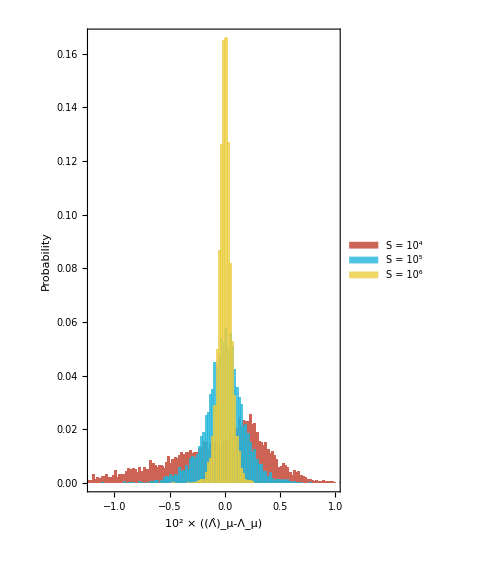

```mathematica
Histogram[100 λt,233,"Probability",PlotRange->{{-1.2,1},{All,All}},ChartLayout->"Overlapped",LabelStyle->{FontFamily->"Lato",14,GrayLevel[0]},ImageSize->Medium,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"Probability",None},{"10^2 × ((Λ̂)_μ-Λ_μ)",None}},PlotLabel->None,ChartLegends->Placed[{"S = 10^4","S = 10^5","S = 10^6"},{.8,.8}],Background->White,AspectRatio->GoldenRatio,ChartStyle->{Directive[Opacity[1],RGBColor["#CD6355"]],Directive[Opacity[.8],RGBColor["#22B6DB"]],Directive[Opacity[.8],RGBColor["#ECCD3E"]]}]
```

We are interested in reconstructing the Pauli error rates of each of the gates as well, and the array pt contains these estimates. Then ptvd computes the total variation distance between the estimated and true Pauli error rates for each gate. We can again plot a histogram to visualize the convergence with increasing S.

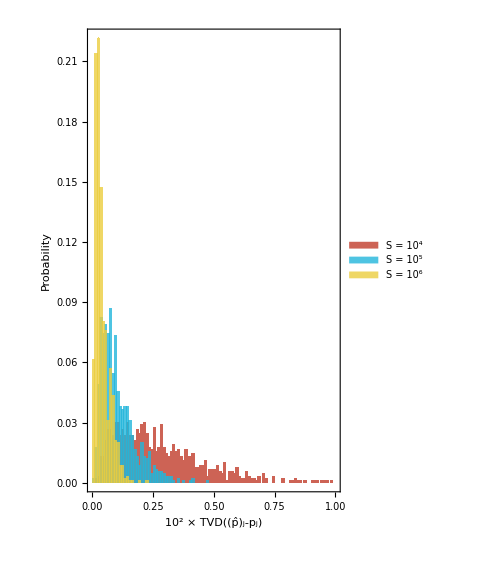

```mathematica
pt=Table[ProbEst[t⟦k⟧,n,1.0/(2 10^(3+k))],{k,kmax}]-ConstantArray[ptrue,3];
ptvd=Table[Total/@(1/2 Abs/@pt⟦k⟧),{k,kmax}];
Histogram[10^2 ptvd,89,"Probability",PlotRange->{{0,1},{All,All}},ChartLayout->"Overlapped",LabelStyle->{FontFamily->"Lato",14,GrayLevel[0]},ImageSize->Medium,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability",None},{"10^2 × TVD((p̂)_j-p_j)",None}},PlotLabel->None,ChartLegends->Placed[{"S = 10^4","S = 10^5","S = 10^6"},{.8,.8}],Background->White,AspectRatio->GoldenRatio,ChartStyle->{Directive[Opacity[1],RGBColor["#CD6355"]],Directive[Opacity[.8],RGBColor["#22B6DB"]],Directive[Opacity[.8],RGBColor["#ECCD3E"]]}]
```